```mathematica
Hz=100*h*Sqrt[e];
e=Ωm(1+z)^3+Ωr(1+z)^4+Ωk(1+z)^2+Ωϕ*(1+z)^(3+3w0+3wa)*E^(-3wa*z/(1+z));
```

```mathematica
DE = 3Ωm(1+z)^2+4Ωr(1+z)^3+2Ωk(1+z)+opp;
opp=3(1+w0+z+w0*z+wa*z)*(1+z)^(1+3w0+3wa)*Ωϕ*E^(-3wa*z/(1+z));
```

```mathematica
H0=100h
```

100 h

```mathematica
gpp=((1+z)*Hz)^2;
gp=(1+z)*Hz^2-(1+z)^2*DE*H0^2/2
g=3/2*Ωm*H0^2*(1+z)^3
```

10000 h^2 (1+z) ((1+z)^2 Ωk+(1+z)^3 Ωm+(1+z)^4 Ωr+ⅇ^(-(3 wa z)/(1+z)) (1+z)^(3+3 w0+3 wa) Ωϕ)-1/2 H0^2 (1+z)^2 (2 (1+z) Ωk+3 (1+z)^2 Ωm+4 (1+z)^3 Ωr+3 ⅇ^(-(3 wa z)/(1+z)) (1+z)^(1+3 w0+3 wa) (1+w0+z+w0 z+wa z) Ωϕ)

3/2 H0^2 (1+z)^3 Ωm

```mathematica
growth1=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]]
growth9=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.675,Ωm->0.246+0.050,Ωϕ->0.704,w0->-0.9,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth11=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.746,Ωm->0.201+0.041,Ωϕ->0.758,w0->-1.1,wa->0,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growthpos=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.776,Ωm->0.186+0.038,Ωϕ->0.766,w0->-1,wa->0,Ωr->0,Ωk->0.01},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growthneg=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.661,Ωm->0.256+0.052,Ωϕ->0.702,w0->-1,wa->0,Ωr->0,Ωk->-0.01},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth5=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->0.5,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
growth15=First[G/.NDSolve[{G''[z]==gp/gpp*G'[z]+g/gpp*G[z]/.{h->0.710,Ωm->0.222+0.045,Ωϕ->0.733,w0->-1,wa->-0.5,Ωr->0,Ωk->0},G[9]==1,G'[9]==-0.1},G,{z,0,9}]];
```

InterpolatingFunction[{{0., 9.}}, <>]

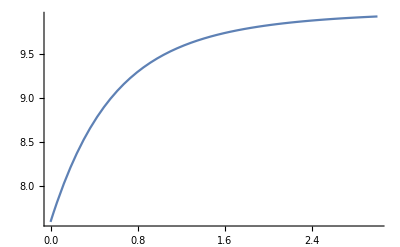

```mathematica
Plot[(1+z)growth1[z],{z,0,3},PlotRange->All]
```

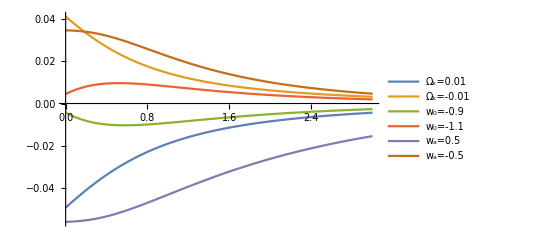

```mathematica
Plot[{(growthpos[z]-growth1[z])/growth1[z],(growthneg[z]-growth1[z])/growth1[z],(growth9[z]-growth1[z])/growth1[z],(growth11[z]-growth1[z])/growth1[z],(growth5[z]-growth1[z])/growth1[z],(growth15[z]-growth1[z])/growth1[z]},{z,0,3},PlotRange->All, PlotLegends->{"Ω_k=0.01","Ω_k=-0.01","w_0=-0.9","w_0=-1.1","w_a=0.5","w_a=-0.5"}]
```

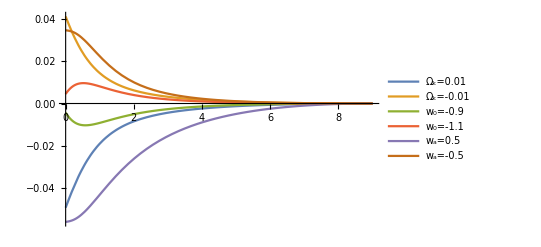

```mathematica
Plot[{(growthpos[z]-growth1[z])/growth1[z],(growthneg[z]-growth1[z])/growth1[z],(growth9[z]-growth1[z])/growth1[z],(growth11[z]-growth1[z])/growth1[z],(growth5[z]-growth1[z])/growth1[z],(growth15[z]-growth1[z])/growth1[z]},{z,0,9},PlotRange->All, PlotLegends->{"Ω_k=0.01","Ω_k=-0.01","w_0=-0.9","w_0=-1.1","w_a=0.5","w_a=-0.5"}]
```

```mathematica
NumberForm[growth1[9-{0,1,2,3,4,5,6,7,8,9,10}/300],20]
```

{1.,1.000333459313274,1.000667125303448,1.001001013827806,1.001335124988841,1.001669458576915,1.002004014287249,1.002338791936922,1.002673791681856,1.003009014221895,1.003344460563066}

```mathematica
theta=First[θ/.NDSolve[{θ''[t]==-0.25*θ'[t]-5.0*Sin[θ[t]],θ[0]==π-0.1,θ'[0]==0},θ,{t,0,10}]]
```

InterpolatingFunction[{{0., 10.}}, <>]

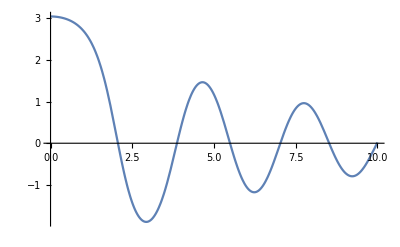

```mathematica
Plot[theta[t],{t,0,10}]
```

```mathematica
a=NumberForm[theta[Range[0,100]/10],9]
```

{3.04159265,3.03910713,3.03161021,3.01885593,3.00034608,2.97531319,2.94269217,2.90108067,2.84868872,2.78327981,2.70210862,2.60186682,2.47865923,2.32805137,2.14525697,1.92556841,1.66515487,1.36231646,1.01910565,0.6428587,0.246763704,-0.151406652,-0.53242157,-0.879327167,-1.18006136,-1.42807039,-1.62130555,-1.76055644,-1.84789005,-1.88553299,-1.87523302,-1.81802441,-1.71432754,-1.56435601,-1.36883333,-1.12999298,-0.852717211,-0.545466911,-0.220487398,0.107128387,0.421441876,0.708022288,0.955705203,1.15720923,1.30871484,1.40890092,1.45793516,1.45671907,1.40650078,1.30886359,1.16605106,0.981550704,0.760788864,0.511689676,0.244783423,-0.0273792574,-0.291483823,-0.535009278,-0.74754441,-0.921468195,-1.05194211,-1.1364438,-1.17415739,-1.16546817,-1.11169344,-1.01508285,-0.879048011,-0.708518507,-0.510260018,-0.292953413,-0.0668672396,0.156908594,0.367504756,0.555286855,0.712556488,0.833813742,0.915645125,0.956411813,0.955920753,0.915204709,0.836462401,0.723141299,0.580088104,0.413650084,0.23159872,0.042786164,-0.1434617,-0.318099284,-0.473076662,-0.601849688,-0.699611665,-0.763281678,-0.791352279,-0.783708891,-0.741501125,-0.667096445,-0.564097101,-0.437361566,-0.292951041,-0.137929514,0.0200120782}

InterpolatingFunction[{{0., 10.}}, <>]

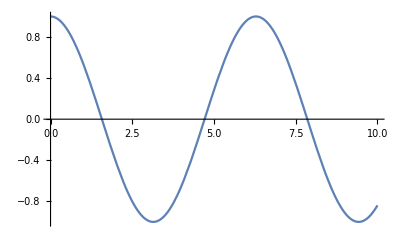

```mathematica
y=First[y/.NDSolve[{y''[t]==-y[t],y[0]==1,y'[0]==0},y,{t,0,10}]]
Plot[y[t],{t,0,10}]
```

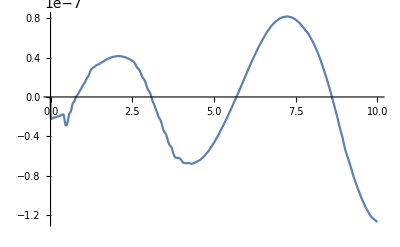

```mathematica
Plot[y[t]-Cos[t],{t,0,10}]
```

```mathematica
NumberForm[Cos[10]//N,20]
```

-0.839071529076452